```mathematica
Needs["NoisyQuantumTeleportationBenchmarking`", FileNameJoin[{NotebookDirectory[],"NoisyQuantumTeleportationBenchmarking.wl"}]]
```

```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`
```

```mathematica
MaTeX["p_a"]
```

MaTeX[p_a]

```mathematica
latexStyle = {FontFamily ->  "LM Roman 12"};
```

```mathematica
contours = Association[{}];
```

```mathematica
Do[AssociateTo[contours,{chA, chB} -> ContourPlot[ResourceNegativityWithChannels[chA[pA], chB[pB]],{pA,0,1},{pB,0,1},
Axes -> True, Frame->False,
AxesLabel->{MaTeX["p_a"], MaTeX["p_b"]}, BaseStyle -> latexStyle
]], {chA, Channels}, {chB, Channels}]
```

```mathematica
labels= MaTeX["\\text{"<>#<>"}"]&/@Table[GetChannelOutputFantasyName[ch], {ch, Channels}];
```

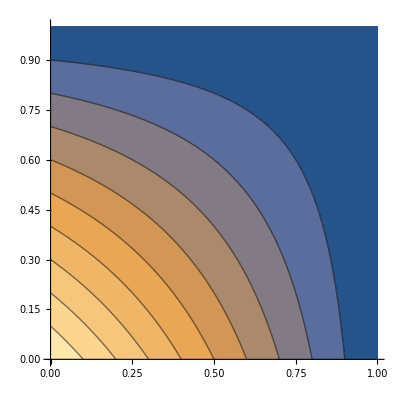
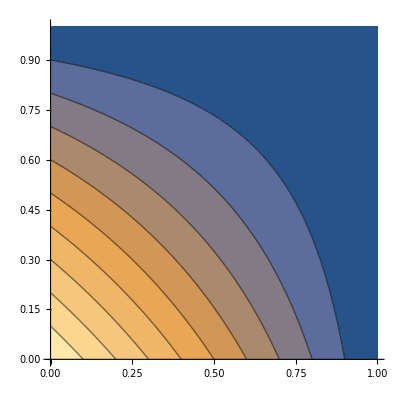
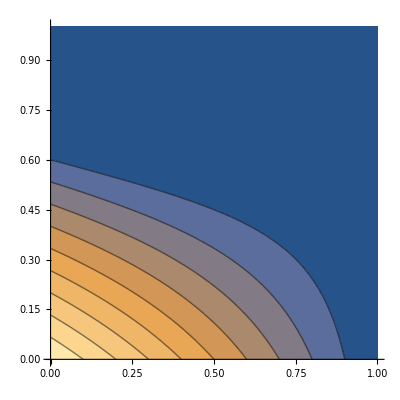
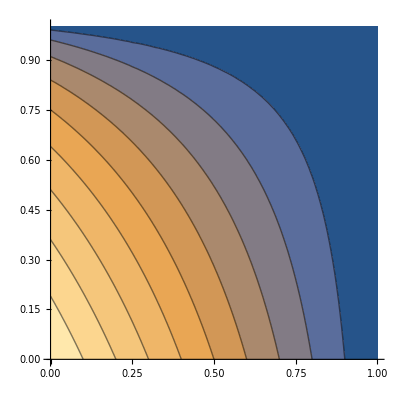
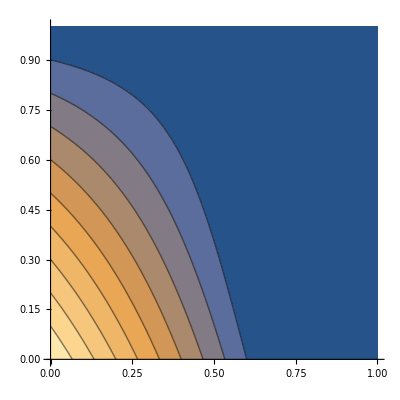
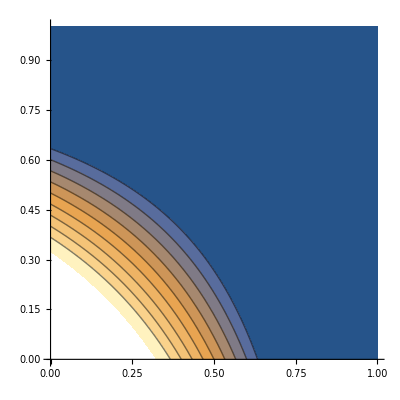
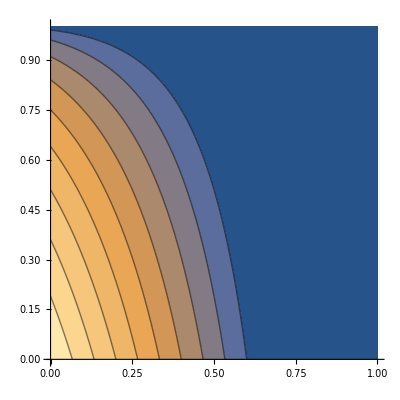
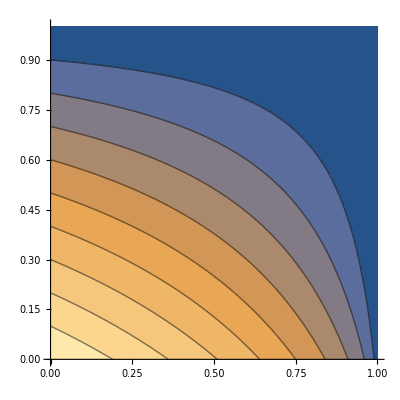
| -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{""}~Join~labels}~Join~Transpose[{Rotate[#,Pi/2]&/@labels}~Join~Transpose[Partition[Values[contours], 4]]]]
```

```mathematica
regions = Association[{}];
```

```mathematica
ForAllChannelsAndDistances[Function[{chA, chB, d, AvgDist}, 
th = GetDistanceThreshold[d];
plot =RegionPlot[{
ChannelsMakeResourceSeparable[chA[pA], chB[pB]] && QuantumCertified[d, AvgDist[pA, pB]], 
!ChannelsMakeResourceSeparable[chA[pA], chB[pB]] && !QuantumCertified[d, AvgDist[pA, pB]]
},{pA,0,1},{pB,0,1},
PlotLabel->"Alice: "<>GetChannelLabel[chA]<>"\nBob: "<>GetChannelLabel[chB]<>"\nDistance: "<>GetDistanceLabel[d]
];

AssociateTo[regions,{chA, chB, d} -> plot];
]]
```

NIntegrate::inumr: The integrand Sin[NoisyQuantumTeleportationBenchmarking`Private`θ] (1/4 (1-pA Cos[NoisyQuantumTeleportationBenchmarking`Private`θ]) √((Cos[«1»]+Times[«3»])^2+(Times[«2»]+Times[«6»])^2+(Times[«2»]+Times[«6»])^2)+1/4 (1+pA Cos[NoisyQuantumTeleportationBenchmarking`Private`θ]) √((Cos[«1»]+Times[«3»])^2+(Times[«2»]+Times[«6»])^2+(Times[«2»]+Times[«6»])^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
plots=Partition[(Show[#, ImageSize -> 200, PlotLabel-> None, AxesLabel->{MaTeX["p_a"], MaTeX["p_b"]}, BaseStyle -> latexStyle, Axes->True, Frame->False])& /@ Values[regions], 4];
```

```mathematica
labelColumnas  = Prepend[MaTeX["\\text{"<>#<>"}"]&/@GetDistanceLabel/@Distances, ""];
labelFilas = MaTeX["\\text{"<>#<>"}"]&/@Flatten[Table["A: "<>GetChannelOutputFantasyName[chA]<>"\nB: "<>GetChannelOutputFantasyName[chB], {chA, Channels}, {chB, Channels}]];
```

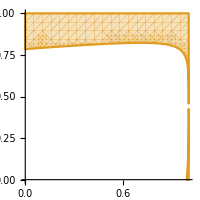
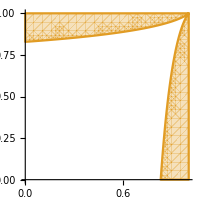
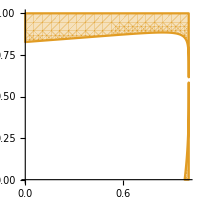
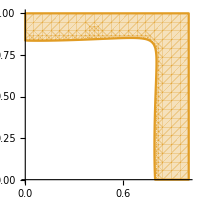
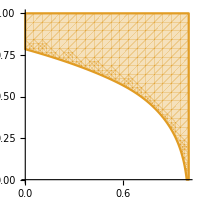
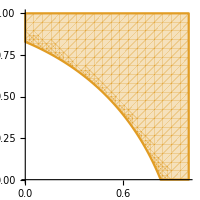
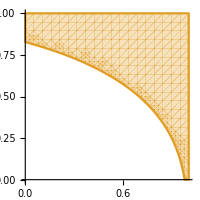
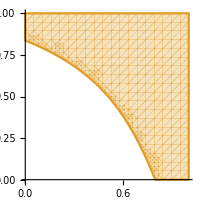
| -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

| -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

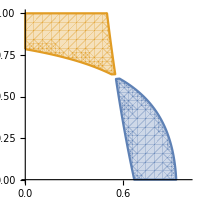
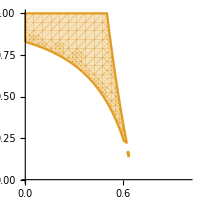
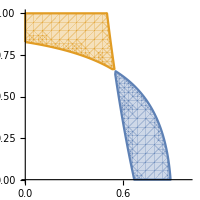
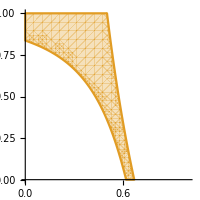
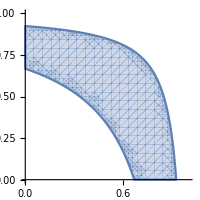
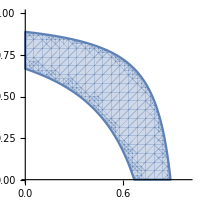
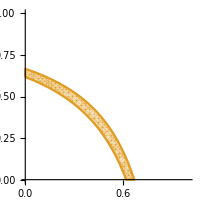
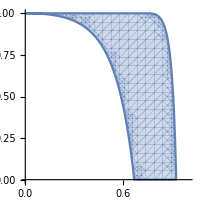
| -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

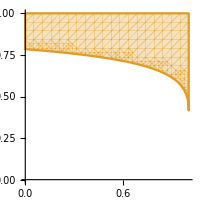
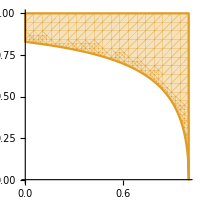
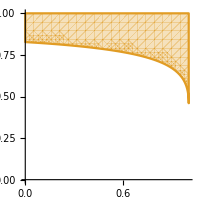
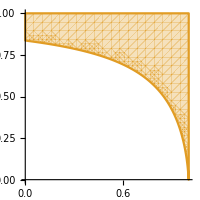
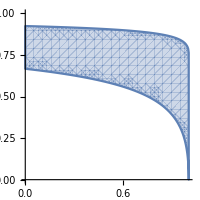
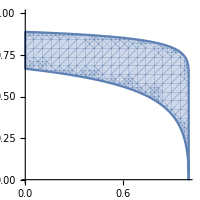
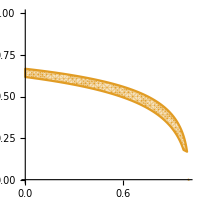
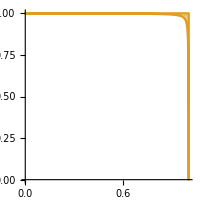
| -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Do[Print[Grid[{labelColumnas}~Join~partition]], {partition, Partition[Transpose[{Rotate[#,Pi/2]&/@labelFilas}~Join~Transpose[plots]], 4]}]
```

```mathematica
Show[regions[{DC, ADC, TrDist}], Axes -> True,ImageSize -> 200, PlotLabel-> None, AxesLabel->{MaTeX["p_a"], MaTeX["p_b"]}, BaseStyle -> latexStyle, Frame->False]
```

-Graphics-